```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/Cambridge_Projects_To_Complete/LSC_Simulations/Example_simulation/bio_LSC

```mathematica
getdata[wavelength_,angle_,side_]:=Module[{import},
import = Import["./side_emission/"<>ToString[wavelength]<>"/"<>ToString[angle]<>"/side_"<>ToString[side]<>"_"<>ToString[angle]<>"_wavelength_"<>ToString[wavelength]<>"_photons_10000.csv"];
If[import===$Failed,Return[{0}];,
Return[import];
];
];
```

```mathematica
(* import data, and export it*) 

endwavelength=451;
startwavelength=449;
angleend=90;
anglestart=1;

(* data store is the directly imported data from the ray tracing. It has dimension of side, angle, then wavelength - BASED ON THE RAYTRACING OPTIONS *) 
datastore=ConstantArray[{},{endwavelength-startwavelength+1,angleend-anglestart+1,4}];
datastore=Table[Tally[Flatten[getdata[wavelength,angle,side]]],{side,1,4,1},{angle,1,90,1},{wavelength,startwavelength,endwavelength,1}];
Export["./datastore.mx",datastore];
```

```mathematica
datastore[[3,1,1]]
```

{{370.,285}}

```mathematica
SetDirectory[NotebookDirectory[]]
endwavelength=451;
startwavelength=449;
angleend=90;
anglestart=1;
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/Cambridge_Projects_To_Complete/LSC_Simulations/Example_simulation/bio_LSC

```mathematica
datastore=Import["./datastore.mx"];
```

```mathematica
mergeLists[x_,y_]:=Module[{f,g,l3},f[{a_,b_}]/;NumericQ[g@a]:=(g[a]+=b);
f[{a_,b_}]:=(g[a]:=b);
l3=Join[x,y];
f/@l3;
{#,g@#}&/@Union[First/@l3]]
```

```mathematica
(* grab last emission wavelength *)
(* 311 nm is always the start *) 
emissionmax=1200;
emissionmin=N[311];
(* wavelength table is used throughout the simulation *) 
wavelengthtable=Table[{N[x],0},{x,emissionmin,emissionmax,1}];
(* account for the zeros, but this will be got rid of - need to account for zeros which came from import *) 
wavelengthtable1=N[Join[{{0,0}},wavelengthtable]];
datastore2=ConstantArray[{},{4,90,Length[wavelengthtable]}];
```

```mathematica
(* this merges the wavelength table (I.e. the range we want to simualte, with the ray tracing data *) 
(* [[2;;]] removes the zeros *) 
(* resulting dimensions are 4 sides, 90 angles, for each RAY TRACING input wavelength *) 
Monitor[WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
Table[
(* if k is greater than 650 nm, then use the refractive value, of k=1 *) 
Which[k>650-emissionmin+1 (*950 - emissionmin*) ,
(* combines the two lists *) 
datastore2[[i,j,k]] =mergeLists[wavelengthtable1,datastore[[i,j,1]]][[2;;,2]];
(* takes the emission part of value of 60, which is where the simulation was run at 370 nm, place this in the correct place*) 
emission =mergeLists[wavelengthtable1,datastore[[i,j,1]]][[2;;]][[60,2]];
datastore2[[i,j,k]][[60]]=0;
(* now need to correct the wavelength *) 
datastore2[[i,j,k]][[k]]=emission;
datastore2[[i,j,k]] =NumericArray[datastore2[[i,j,k]] ,"Real32"];, 
k<=500-emissionmin, 
 (* if it is less, use k=3, the PM raytracing results *) 
datastore2[[i,j,k]] =mergeLists[wavelengthtable1,datastore[[i,j,3]]][[2;;,2]];
datastore2[[i,j,k]] =NumericArray[datastore2[[i,j,k]] ,"Real32"];, 
500-emissionmin<k<= 650-emissionmin+1 , 
(* if the wavelength is inbetween, use k=2, the dot raytracing results *) 
datastore2[[i,j,k]] =mergeLists[wavelengthtable1,datastore[[i,j,2]]][[2;;,2]];
datastore2[[i,j,k]] =NumericArray[datastore2[[i,j,k]] ,"Real32"];
],
{i,1,4,1},{j,1,90,1},{k,1,Length[wavelengthtable],1}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]],{i,j,k}]
```

```mathematica
DumpSave["./datastore2.mx",datastore2];
```

```mathematica
raytracingdata=datastore2;
DumpSave["./raytracing.mx",raytracingdata];
```

```mathematica
Import["datastore2.mx"]
```

```mathematica
endwavelength=550;
startwavelength=370;
```

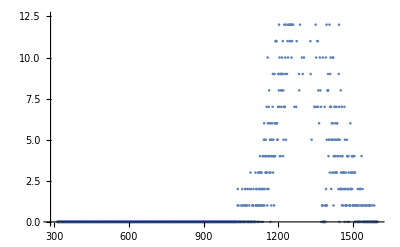

```mathematica
ListPlot[Transpose[{wavelengthtable[[;;,1]],data2}]]
```

```mathematica
Table[#[[x]]&/@datastore2[[1,95, 500]],{x,Range[Length[890]]}]
```

{}

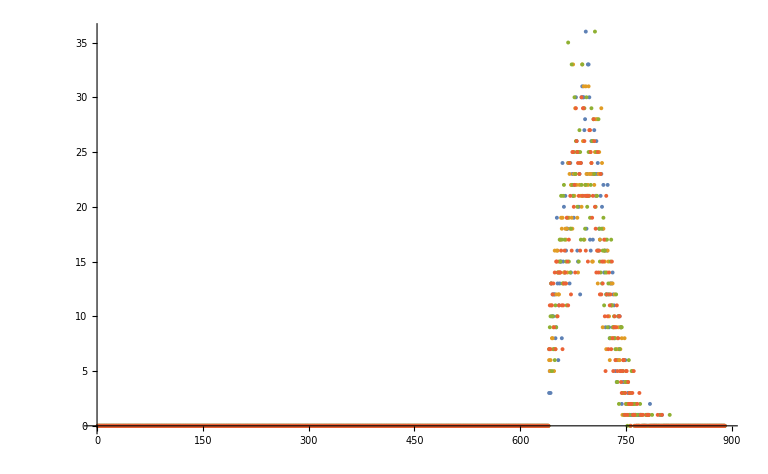

```mathematica
ListPlot[Transpose[Table[#[[x]]&/@Normal[datastore2[[;;,88, 200]]],{x,Range[890]}]]]
```

```mathematica
Dimensions[datastore2]
```

{4,90,890}

```mathematica
datastore2[[1,90, 500]]
```

NumericArray[…]

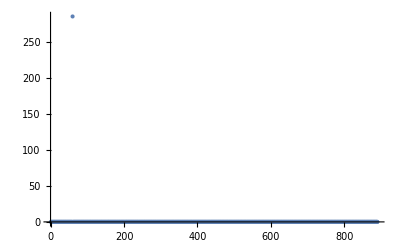

```mathematica
ListPlot[Total[#]&/@Table[#[[x]]&/@datastore2[[;;,1, 890]],{x,Range[890]}]]
```

```mathematica
raytracingdata=datastore2;
```

```mathematica
emissionmax=1600;
```

```mathematica
incidentangle=80;
totalphotonsin=10000;
wavelength0=311;
```

```mathematica
raytracingdata[[1,incidentangle,5,]]
```

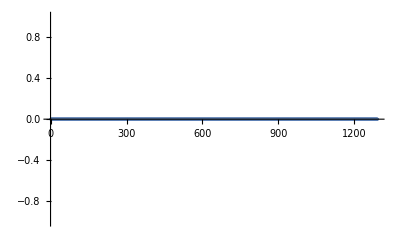

```mathematica
ListPlot[5*Normal[raytracingdata[[1,incidentangle,300-wavelength0+1]]]]
```

```mathematica
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
LSCoutputlistdirect=Table[{wlength,1/(totalphotonsin)*1*Normal[raytracingdata[[1,incidentangle,wlength-wavelength0+1]]]} , {wlength, emissionmin, emissionmax,1}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]]
```

```mathematica
LSCoutputlistdirect=NumericArray[LSCoutputlistdirect[[;;,2]],"Real32"];
```

```mathematica
LSCoutputlistdirect=Total[LSCoutputlistdirect];
```

```mathematica
LSCoutputlistdirect;
```

```mathematica
incidentangle
```

80

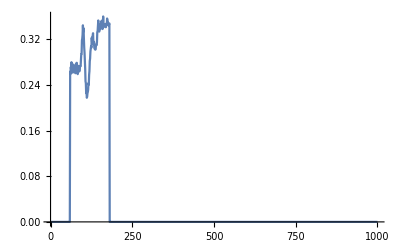

```mathematica
ListPlot[Table[Total[LSCoutputlistdirect[[x,2]]],{x,1,1000,1}],Joined->True]
```

```mathematica
outputmatrix =LSCoutputlistdirect[[;;,2]];
```

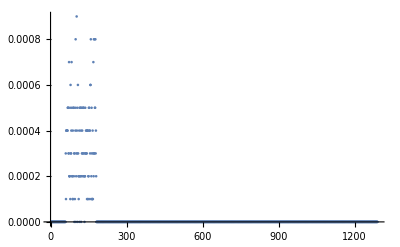

```mathematica
ListPlot[outputmatrix[[;;,850]]]
```

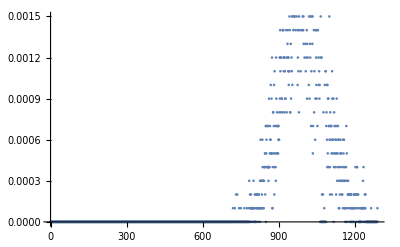

```mathematica
ListPlot[outputmatrix[[100]]]
```

```mathematica
anglerange = Join[Range[1,incidentangle-1,1],Range[incidentangle+1,90,1]];
```

```mathematica
side=1;
```

```mathematica
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
LSCoutputlistdiffuse=Table[{wlength,1/(totalphotonsin)*Normal[raytracingdata[[side,angle,wlength-wavelength0+1]]]} , {wlength, emissionmin, emissionmax,1},{angle,anglerange}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]];
```

```mathematica
Dimensions[LSCoutputlistdiffuse]
```

{1290,89,2}

```mathematica
(* Now, LSCoutputlistdiffuse in terms in {input wavelenglth,angle,{output spectra}}, what we need is the total output spectra {nm out, total}  *) 
outputmatrix =LSCoutputlistdiffuse[[;;,;;,2]];
sidespectrafluxdirect=Table[{λ,Total[outputmatrix[[;;,;;,λ-wavelength0+1]],2]},{λ,wavelengthtable[[;;,1]]}];(*nm,A/(nm m^2)*)
```

```mathematica
sidespectrafluxdirect
```

{{311.,0.},{312.,0.},{313.,0.},{314.,0.},{315.,0.},{316.,0.},{317.,0.},{318.,0.},{319.,0.},{320.,0.},{321.,0.},{322.,0.},{323.,0.},{324.,0.},{325.,0.},{326.,0.},{327.,0.},{328.,0.},{329.,0.},{330.,0.},{331.,0.},{332.,0.},{333.,0.},{334.,0.},{335.,0.},{336.,0.},{337.,0.},{338.,0.},{339.,0.},{340.,0.},{341.,0.},{342.,0.},{343.,0.},{344.,0.},{345.,0.},{346.,0.},{347.,0.},{348.,0.},{349.,0.},{350.,0.},{351.,0.},{352.,0.},{353.,0.},{354.,0.},{355.,0.},{356.,0.},{357.,0.},{358.,0.},{359.,0.},{360.,0.},{361.,0.},{362.,0.},{363.,0.},{364.,0.},{365.,0.},{366.,0.},{367.,0.},{368.,0.},{369.,0.},{370.,0.},{371.,0.},{372.,0.},{373.,0.},{374.,0.},{375.,0.},{376.,0.},{377.,0.},{378.,0.},{379.,0.},{380.,0.},{381.,0.},{382.,0.},{383.,0.},{384.,0.},{385.,0.},{386.,0.},{387.,0.},{388.,0.},{389.,0.},{390.,0.},{391.,0.},{392.,0.},{393.,0.},{394.,0.},{395.,0.},{396.,0.},{397.,0.},{398.,0.},{399.,0.},{400.,0.},{401.,0.},{402.,0.},{403.,0.},{404.,0.},{405.,0.},{406.,0.},{407.,0.},{408.,0.},{409.,0.},{410.,0.},{411.,0.},{412.,0.},{413.,0.},{414.,0.},{415.,0.},{416.,0.},{417.,0.},{418.,0.},{419.,0.},{420.,0.},{421.,0.},{422.,0.},{423.,0.},{424.,0.},{425.,0.},{426.,0.},{427.,0.},{428.,0.},{429.,0.},{430.,0.},{431.,0.},{432.,0.},{433.,0.},{434.,0.},{435.,0.},{436.,0.},{437.,0.},{438.,0.},{439.,0.},{440.,0.},{441.,0.},{442.,0.},{443.,0.},{444.,0.},{445.,0.},{446.,0.},{447.,0.},{448.,0.},{449.,0.},{450.,0.},{451.,0.},{452.,0.},{453.,0.},{454.,0.},{455.,0.},{456.,0.},{457.,0.},{458.,0.},{459.,0.},{460.,0.},{461.,0.},{462.,0.},{463.,0.},{464.,0.},{465.,0.},{466.,0.},{467.,0.},{468.,0.},{469.,0.},{470.,0.},{471.,0.},{472.,0.},{473.,0.},{474.,0.},{475.,0.},{476.,0.},{477.,0.},{478.,0.},{479.,0.},{480.,0.},{481.,0.},{482.,0.},{483.,0.},{484.,0.},{485.,0.},{486.,0.},{487.,0.},{488.,0.},{489.,0.},{490.,0.},{491.,0.},{492.,0.},{493.,0.},{494.,0.},{495.,0.},{496.,0.},{497.,0.},{498.,0.},{499.,0.},{500.,0.},{501.,0.},{502.,0.},{503.,0.},{504.,0.},{505.,0.},{506.,0.},{507.,0.},{508.,0.},{509.,0.},{510.,0.},{511.,0.},{512.,0.},{513.,0.},{514.,0.},{515.,0.},{516.,0.},{517.,0.},{518.,0.},{519.,0.},{520.,0.},{521.,0.},{522.,0.},{523.,0.},{524.,0.},{525.,0.},{526.,0.},{527.,0.},{528.,0.},{529.,0.},{530.,0.},{531.,0.},{532.,0.},{533.,0.},{534.,0.},{535.,0.},{536.,0.},{537.,0.},{538.,0.},{539.,0.},{540.,0.},{541.,0.},{542.,0.},{543.,0.},{544.,0.},{545.,0.},{546.,0.},{547.,0.},{548.,0.},{549.,0.},{550.,0.},{551.,0.},{552.,0.},{553.,0.},{554.,0.},{555.,0.},{556.,0.},{557.,0.},{558.,0.},{559.,0.},{560.,0.},{561.,0.},{562.,0.},{563.,0.},{564.,0.},{565.,0.},{566.,0.},{567.,0.},{568.,0.},{569.,0.},{570.,0.},{571.,0.},{572.,0.},{573.,0.},{574.,0.},{575.,0.},{576.,0.},{577.,0.},{578.,0.},{579.,0.},{580.,0.},{581.,0.},{582.,0.},{583.,0.},{584.,0.},{585.,0.},{586.,0.},{587.,0.},{588.,0.},{589.,0.},{590.,0.},{591.,0.},{592.,0.},{593.,0.},{594.,0.},{595.,0.},{596.,0.},{597.,0.},{598.,0.},{599.,0.},{600.,0.},{601.,0.},{602.,0.},{603.,0.},{604.,0.},{605.,0.},{606.,0.},{607.,0.},{608.,0.},{609.,0.},{610.,0.},{611.,0.},{612.,0.},{613.,0.},{614.,0.},{615.,0.},{616.,0.},{617.,0.},{618.,0.},{619.,0.},{620.,0.},{621.,0.},{622.,0.},{623.,0.},{624.,0.},{625.,0.},{626.,0.},{627.,0.},{628.,0.},{629.,0.},{630.,0.},{631.,0.},{632.,0.},{633.,0.},{634.,0.},{635.,0.},{636.,0.},{637.,0.},{638.,0.},{639.,0.},{640.,0.},{641.,0.},{642.,0.},{643.,0.},{644.,0.},{645.,0.},{646.,0.},{647.,0.},{648.,0.},{649.,0.},{650.,0.},{651.,0.},{652.,0.},{653.,0.},{654.,0.},{655.,0.},{656.,0.},{657.,0.},{658.,0.},{659.,0.},{660.,0.},{661.,0.},{662.,0.},{663.,0.},{664.,0.},{665.,0.},{666.,0.},{667.,0.},{668.,0.},{669.,0.},{670.,0.},{671.,0.},{672.,0.},{673.,0.},{674.,0.},{675.,0.},{676.,0.},{677.,0.},{678.,0.},{679.,0.},{680.,0.},{681.,0.},{682.,0.},{683.,0.},{684.,0.},{685.,0.},{686.,0.},{687.,0.},{688.,0.},{689.,0.},{690.,0.},{691.,0.},{692.,0.},{693.,0.},{694.,0.},{695.,0.},{696.,0.},{697.,0.},{698.,0.},{699.,0.},{700.,0.},{701.,0.},{702.,0.},{703.,0.},{704.,0.},{705.,0.},{706.,0.},{707.,0.},{708.,0.},{709.,0.},{710.,0.},{711.,0.},{712.,0.},{713.,0.},{714.,0.},{715.,0.},{716.,0.},{717.,0.},{718.,0.},{719.,0.},{720.,0.},{721.,0.},{722.,0.},{723.,0.},{724.,0.},{725.,0.},{726.,0.},{727.,0.},{728.,0.},{729.,0.},{730.,0.},{731.,0.},{732.,0.},{733.,0.},{734.,0.},{735.,0.},{736.,0.},{737.,0.},{738.,0.},{739.,0.},{740.,0.},{741.,0.},{742.,0.},{743.,0.},{744.,0.},{745.,0.},{746.,0.},{747.,0.},{748.,0.},{749.,0.},{750.,0.},{751.,0.},{752.,0.},{753.,0.},{754.,0.},{755.,0.},{756.,0.},{757.,0.},{758.,0.},{759.,0.},{760.,0.},{761.,0.},{762.,0.},{763.,0.},{764.,0.},{765.,0.},{766.,0.},{767.,0.},{768.,0.},{769.,0.},{770.,0.},{771.,0.},{772.,0.},{773.,0.},{774.,0.},{775.,0.},{776.,0.},{777.,0.},{778.,0.},{779.,0.},{780.,0.},{781.,0.},{782.,0.},{783.,0.},{784.,0.},{785.,0.},{786.,0.},{787.,0.},{788.,0.},{789.,0.},{790.,0.},{791.,0.},{792.,0.},{793.,0.},{794.,0.},{795.,0.},{796.,0.},{797.,0.},{798.,0.},{799.,0.},{800.,0.},{801.,0.},{802.,0.},{803.,0.},{804.,0.},{805.,0.},{806.,0.},{807.,0.},{808.,0.},{809.,0.},{810.,0.},{811.,0.},{812.,0.},{813.,0.},{814.,0.},{815.,0.},{816.,0.},{817.,0.},{818.,0.},{819.,0.},{820.,0.},{821.,0.},{822.,0.},{823.,0.},{824.,0.},{825.,0.},{826.,0.},{827.,0.},{828.,0.},{829.,0.},{830.,0.},{831.,0.},{832.,0.},{833.,0.},{834.,0.},{835.,0.},{836.,0.},{837.,0.},{838.,0.},{839.,0.},{840.,0.},{841.,0.},{842.,0.},{843.,0.},{844.,0.},{845.,0.},{846.,0.},{847.,0.},{848.,0.},{849.,0.},{850.,0.},{851.,0.},{852.,0.},{853.,0.},{854.,0.},{855.,0.},{856.,0.},{857.,0.},{858.,0.},{859.,0.},{860.,0.},{861.,0.},{862.,0.},{863.,0.},{864.,0.},{865.,0.},{866.,0.},{867.,0.},{868.,0.},{869.,0.},{870.,0.},{871.,0.},{872.,0.},{873.,0.},{874.,0.},{875.,0.},{876.,0.},{877.,0.},{878.,0.},{879.,0.},{880.,0.},{881.,0.},{882.,0.},{883.,0.},{884.,0.},{885.,0.},{886.,0.},{887.,0.},{888.,0.},{889.,0.},{890.,0.},{891.,0.},{892.,0.},{893.,0.},{894.,0.},{895.,0.},{896.,0.},{897.,0.},{898.,0.},{899.,0.},{900.,0.},{901.,0.},{902.,0.},{903.,0.},{904.,0.},{905.,0.},{906.,0.},{907.,0.},{908.,0.},{909.,0.},{910.,0.},{911.,0.},{912.,0.},{913.,0.},{914.,0.},{915.,0.},{916.,0.},{917.,0.},{918.,0.},{919.,0.},{920.,0.},{921.,0.},{922.,0.},{923.,0.},{924.,0.},{925.,0.},{926.,0.},{927.,0.},{928.,0.},{929.,0.},{930.,0.},{931.,0.},{932.,0.},{933.,0.},{934.,0.},{935.,0.},{936.,0.},{937.,0.},{938.,0.},{939.,0.},{940.,0.},{941.,0.},{942.,0.},{943.,0.},{944.,0.},{945.,0.},{946.,0.},{947.,0.},{948.,0.},{949.,0.},{950.,0.},{951.,0.},{952.,0.},{953.,0.},{954.,0.},{955.,0.},{956.,0.},{957.,0.},{958.,0.},{959.,0.},{960.,0.},{961.,0.},{962.,0.},{963.,0.},{964.,0.},{965.,0.},{966.,0.},{967.,0.},{968.,0.},{969.,0.},{970.,0.},{971.,0.},{972.,0.},{973.,0.},{974.,0.},{975.,0.},{976.,0.},{977.,0.},{978.,0.},{979.,0.},{980.,0.},{981.,0.},{982.,0.},{983.,0.},{984.,0.},{985.,0.},{986.,0.},{987.,0.},{988.,0.},{989.,0.},{990.,0.},{991.,0.},{992.,0.},{993.,0.},{994.,0.},{995.,0.},{996.,0.},{997.,0.},{998.,0.},{999.,0.},{1000.,0.0528},{1001.,0.0718},{1002.,0.0738},{1003.,0.0782},{1004.,0.0514},{1005.,0.0276},{1006.,0.0302},{1007.,0.0176},{1008.,0.0141},{1009.,0.0502},{1010.,0.0438},{1011.,0.0123},{1012.,0.0069},{1013.,0.0252},{1014.,0.0027},{1015.,0.},{1016.,0.0332},{1017.,0.024},{1018.,0.0476},{1019.,0.0643},{1020.,0.0648},{1021.,0.0386},{1022.,0.0145},{1023.,0.0441},{1024.,0.0599},{1025.,0.0458},{1026.,0.0221},{1027.,0.0017},{1028.,0.0373},{1029.,0.0535},{1030.,0.0761},{1031.,0.0928},{1032.,0.0933},{1033.,0.0495},{1034.,0.0286},{1035.,0.0353},{1036.,0.0898},{1037.,0.1048},{1038.,0.088},{1039.,0.0801},{1040.,0.0777},{1041.,0.1304},{1042.,0.1444},{1043.,0.1415},{1044.,0.1659},{1045.,0.1285},{1046.,0.1185},{1047.,0.0749},{1048.,0.0894},{1049.,0.0957},{1050.,0.1068},{1051.,0.1252},{1052.,0.1335},{1053.,0.1525},{1054.,0.1645},{1055.,0.1694},{1056.,0.1783},{1057.,0.1677},{1058.,0.151},{1059.,0.1233},{1060.,0.0915},{1061.,0.1413},{1062.,0.1666},{1063.,0.1775},{1064.,0.1761},{1065.,0.1895},{1066.,0.1875},{1067.,0.185},{1068.,0.2221},{1069.,0.2206},{1070.,0.2205},{1071.,0.2084},{1072.,0.2245},{1073.,0.2093},{1074.,0.2394},{1075.,0.2438},{1076.,0.2455},{1077.,0.255},{1078.,0.2588},{1079.,0.29},{1080.,0.2834},{1081.,0.3185},{1082.,0.319},{1083.,0.3226},{1084.,0.2997},{1085.,0.3148},{1086.,0.3424},{1087.,0.3442},{1088.,0.3645},{1089.,0.3706},{1090.,0.3821},{1091.,0.3946},{1092.,0.3682},{1093.,0.3896},{1094.,0.4038},{1095.,0.4332},{1096.,0.4839},{1097.,0.5262},{1098.,0.5166},{1099.,0.5196},{1100.,0.5646},{1101.,0.5894},{1102.,0.5957},{1103.,0.6327},{1104.,0.6646},{1105.,0.6736},{1106.,0.6971},{1107.,0.6925},{1108.,0.7199},{1109.,0.7435},{1110.,0.789},{1111.,0.7789},{1112.,0.7977},{1113.,0.8502},{1114.,0.8376},{1115.,0.819},{1116.,0.8465},{1117.,0.8969},{1118.,0.957},{1119.,0.9689},{1120.,1.014},{1121.,1.0394},{1122.,1.0734},{1123.,1.1095},{1124.,1.1149},{1125.,1.1338},{1126.,1.1935},{1127.,1.2587},{1128.,1.3083},{1129.,1.3651},{1130.,1.4221},{1131.,1.4622},{1132.,1.4394},{1133.,1.5264},{1134.,1.5573},{1135.,1.5959},{1136.,1.6478},{1137.,1.6945},{1138.,1.7355},{1139.,1.8056},{1140.,1.8873},{1141.,1.9213},{1142.,1.9386},{1143.,1.9425},{1144.,1.9949},{1145.,2.0167},{1146.,2.1637},{1147.,2.2296},{1148.,2.2354},{1149.,2.3121},{1150.,2.3412},{1151.,2.4876},{1152.,2.5453},{1153.,2.6301},{1154.,2.6096},{1155.,2.7599},{1156.,2.7988},{1157.,2.8589},{1158.,2.8594},{1159.,2.8351},{1160.,3.1126},{1161.,3.1513},{1162.,3.2513},{1163.,3.1571},{1164.,3.2197},{1165.,3.288},{1166.,3.5181},{1167.,3.5575},{1168.,3.5589},{1169.,3.6419},{1170.,3.6264},{1171.,3.8005},{1172.,3.9199},{1173.,3.9172},{1174.,4.1573},{1175.,4.0538},{1176.,4.2539},{1177.,4.2483},{1178.,4.2991},{1179.,4.4524},{1180.,4.74},{1181.,4.4664},{1182.,4.7376},{1183.,4.8341},{1184.,4.8741},{1185.,5.1437},{1186.,5.1992},{1187.,5.1287},{1188.,5.2249},{1189.,5.3139},{1190.,5.3615},{1191.,5.3908},{1192.,5.6734},{1193.,5.5979},{1194.,5.723},{1195.,5.8332},{1196.,5.903},{1197.,5.9858},{1198.,6.1398},{1199.,6.2203},{1200.,6.2828},{1201.,6.5045},{1202.,6.491},{1203.,6.5645},{1204.,6.6235},{1205.,6.7408},{1206.,6.8828},{1207.,6.7988},{1208.,6.9649},{1209.,7.0635},{1210.,7.1713},{1211.,7.2859},{1212.,7.151},{1213.,7.3075},{1214.,7.4556},{1215.,7.3648},{1216.,7.5542},{1217.,7.665},{1218.,7.833},{1219.,7.9743},{1220.,8.0448},{1221.,8.2343},{1222.,8.1837},{1223.,8.0447},{1224.,8.2979},{1225.,8.5059},{1226.,8.6289},{1227.,8.6379},{1228.,8.9845},{1229.,8.9794},{1230.,9.0963},{1231.,9.215},{1232.,9.1987},{1233.,9.2959},{1234.,9.521},{1235.,9.6752},{1236.,9.612},{1237.,9.7045},{1238.,9.8638},{1239.,9.9857},{1240.,10.2868},{1241.,10.2893},{1242.,10.4147},{1243.,10.4691},{1244.,10.4092},{1245.,10.412},{1246.,10.6936},{1247.,10.8694},{1248.,10.8901},{1249.,10.9259},{1250.,10.911},{1251.,10.9288},{1252.,11.1859},{1253.,11.3587},{1254.,11.2859},{1255.,11.405},{1256.,11.5102},{1257.,11.5648},{1258.,11.8191},{1259.,11.6346},{1260.,11.6012},{1261.,12.0271},{1262.,11.9672},{1263.,11.919},{1264.,12.2402},{1265.,12.0556},{1266.,12.0409},{1267.,12.4185},{1268.,12.5067},{1269.,12.7363},{1270.,12.8099},{1271.,12.8511},{1272.,12.653},{1273.,12.727},{1274.,12.8678},{1275.,12.7665},{1276.,12.6892},{1277.,12.7058},{1278.,12.988},{1279.,13.0168},{1280.,13.1826},{1281.,13.027},{1282.,12.9478},{1283.,13.3464},{1284.,13.4441},{1285.,13.4465},{1286.,13.269},{1287.,13.2055},{1288.,13.2399},{1289.,13.4671},{1290.,13.5959},{1291.,13.5651},{1292.,13.4872},{1293.,13.5559},{1294.,13.411},{1295.,13.3163},{1296.,13.4384},{1297.,13.3671},{1298.,13.4685},{1299.,13.46},{1300.,13.6165},{1301.,13.3807},{1302.,13.6283},{1303.,13.5103},{1304.,13.4516},{1305.,13.4195},{1306.,13.2681},{1307.,13.2785},{1308.,13.2366},{1309.,13.2205},{1310.,13.3938},{1311.,13.3401},{1312.,13.2106},{1313.,13.1757},{1314.,13.229},{1315.,13.2927},{1316.,13.2949},{1317.,13.0375},{1318.,12.8525},{1319.,13.1624},{1320.,13.2053},{1321.,13.106},{1322.,12.7795},{1323.,13.12},{1324.,13.2504},{1325.,13.0846},{1326.,12.5791},{1327.,12.6446},{1328.,12.62},{1329.,12.9732},{1330.,12.8881},{1331.,12.6693},{1332.,12.5394},{1333.,12.2692},{1334.,12.4564},{1335.,12.286},{1336.,12.1084},{1337.,12.2345},{1338.,12.1384},{1339.,12.3911},{1340.,12.1412},{1341.,11.9709},{1342.,11.9815},{1343.,11.5803},{1344.,11.8724},{1345.,11.6144},{1346.,11.6971},{1347.,11.4706},{1348.,11.5654},{1349.,11.2776},{1350.,11.4333},{1351.,11.3824},{1352.,11.192},{1353.,10.9602},{1354.,11.0446},{1355.,11.0957},{1356.,10.9449},{1357.,10.6029},{1358.,10.5464},{1359.,10.5053},{1360.,10.3441},{1361.,10.4497},{1362.,10.087},{1363.,10.2788},{1364.,10.6665},{1365.,9.6485},{1366.,9.8449},{1367.,10.0111},{1368.,9.7842},{1369.,9.8983},{1370.,9.854},{1371.,9.4271},{1372.,9.4197},{1373.,9.5751},{1374.,0.4196},{1375.,9.7556},{1376.,9.699},{1377.,0.4047},{1378.,0.3966},{1379.,0.4064},{1380.,9.4976},{1381.,0.4018},{1382.,0.394},{1383.,0.3743},{1384.,0.3801},{1385.,0.37},{1386.,0.3745},{1387.,8.7633},{1388.,0.3673},{1389.,0.3476},{1390.,0.3635},{1391.,0.3534},{1392.,8.1255},{1393.,0.3409},{1394.,0.3404},{1395.,7.5779},{1396.,7.6692},{1397.,0.311},{1398.,7.6014},{1399.,7.5927},{1400.,7.331},{1401.,6.9803},{1402.,7.086},{1403.,6.9415},{1404.,6.7396},{1405.,6.6986},{1406.,6.4227},{1407.,6.4645},{1408.,6.2038},{1409.,6.0942},{1410.,5.8707},{1411.,5.7302},{1412.,5.6568},{1413.,5.552},{1414.,5.4223},{1415.,5.3024},{1416.,5.3293},{1417.,5.1704},{1418.,4.949},{1419.,4.9928},{1420.,4.8837},{1421.,4.6481},{1422.,4.6687},{1423.,4.5938},{1424.,4.6005},{1425.,4.4467},{1426.,4.4433},{1427.,4.4908},{1428.,4.4735},{1429.,4.429},{1430.,4.334},{1431.,4.1921},{1432.,4.3068},{1433.,4.3082},{1434.,4.0845},{1435.,4.209},{1436.,4.2457},{1437.,4.1646},{1438.,4.0323},{1439.,3.8827},{1440.,3.8994},{1441.,3.85},{1442.,3.8188},{1443.,3.6533},{1444.,3.6235},{1445.,3.6531},{1446.,3.5414},{1447.,3.3922},{1448.,3.3866},{1449.,3.3736},{1450.,3.352},{1451.,3.2499},{1452.,3.1715},{1453.,3.181},{1454.,3.111},{1455.,3.0595},{1456.,3.0029},{1457.,2.9239},{1458.,2.8516},{1459.,2.8531},{1460.,2.7635},{1461.,2.7012},{1462.,2.6244},{1463.,2.5924},{1464.,2.55},{1465.,2.5198},{1466.,2.4682},{1467.,2.4434},{1468.,2.3631},{1469.,2.359},{1470.,2.2717},{1471.,2.2053},{1472.,2.173},{1473.,2.1893},{1474.,2.112},{1475.,2.048},{1476.,2.0353},{1477.,1.9619},{1478.,1.9519},{1479.,1.8347},{1480.,1.8945},{1481.,1.8816},{1482.,1.7963},{1483.,1.754},{1484.,1.7213},{1485.,1.7743},{1486.,1.6821},{1487.,1.6477},{1488.,1.6264},{1489.,1.5604},{1490.,1.5148},{1491.,1.4637},{1492.,1.4395},{1493.,1.423},{1494.,1.4073},{1495.,1.3666},{1496.,1.3204},{1497.,1.2941},{1498.,1.2782},{1499.,1.24},{1500.,1.1933},{1501.,1.1625},{1502.,1.1714},{1503.,1.1201},{1504.,1.09},{1505.,1.0993},{1506.,1.0867},{1507.,1.0762},{1508.,1.053},{1509.,1.0201},{1510.,1.02},{1511.,0.9788},{1512.,0.9278},{1513.,0.8979},{1514.,0.846},{1515.,0.8412},{1516.,0.8452},{1517.,0.8058},{1518.,0.8189},{1519.,0.7812},{1520.,0.7327},{1521.,0.7208},{1522.,0.6944},{1523.,0.7182},{1524.,0.6631},{1525.,0.6094},{1526.,0.6252},{1527.,0.6064},{1528.,0.6385},{1529.,0.6563},{1530.,0.6047},{1531.,0.5658},{1532.,0.5743},{1533.,0.5683},{1534.,0.6321},{1535.,0.6314},{1536.,0.5708},{1537.,0.5225},{1538.,0.5035},{1539.,0.5181},{1540.,0.4908},{1541.,0.4829},{1542.,0.4789},{1543.,0.4974},{1544.,0.4767},{1545.,0.4656},{1546.,0.446},{1547.,0.4205},{1548.,0.3926},{1549.,0.4114},{1550.,0.3981},{1551.,0.4072},{1552.,0.3625},{1553.,0.3386},{1554.,0.2975},{1555.,0.3025},{1556.,0.2779},{1557.,0.2991},{1558.,0.3241},{1559.,0.3033},{1560.,0.2915},{1561.,0.2579},{1562.,0.2668},{1563.,0.2757},{1564.,0.2954},{1565.,0.2857},{1566.,0.2455},{1567.,0.2537},{1568.,0.2167},{1569.,0.2224},{1570.,0.2177},{1571.,0.2512},{1572.,0.2412},{1573.,0.2248},{1574.,0.2249},{1575.,0.2453},{1576.,0.207},{1577.,0.1914},{1578.,0.1703},{1579.,0.1727},{1580.,0.1364},{1581.,0.1099},{1582.,0.0981},{1583.,0.1144},{1584.,0.1066},{1585.,0.1461},{1586.,0.1329},{1587.,0.0912},{1588.,0.0701},{1589.,0.0707},{1590.,0.0909},{1591.,0.096},{1592.,0.1152},{1593.,0.0903},{1594.,0.0163},{1595.,0.0656},{1596.,0.1292},{1597.,0.0793},{1598.,0.0266},{1599.,0.0045},{1600.,0.1083}}